Initial Conditions:

```mathematica
basis={{1,0},{0.5,Sqrt[3]/2}}; (* A basis generating the lattice points. Length equal to dimension of lattice.*)
c={0,0,0,0,0,0,0,1,0,0,0,1,0,0,0}; (* Initial conditions. *)
rowLength[n_Integer]:=If[EvenQ[n],{n/2,n/2},{(n+1)/2,(n-1)/2}]; (*Specifies how many "odd" and "even" triangles are in our graphic. First value is odd trangles. *)
```

Triangular Cells 1D Case:

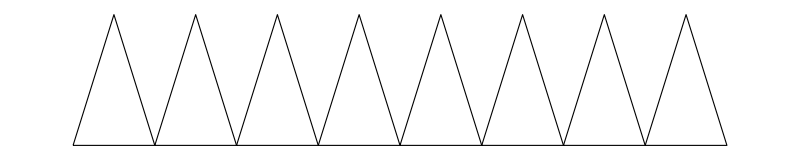

```mathematica
oddTriangles[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],r=rowLength[Length[initialConditions]][[1]]-1},
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*i+1]]]],EdgeForm[Black],Triangle[{i*b1,(i+1)*b1,i*b1+b2}]},
{i,0,r}]
]; (* Generates the "odd" traingles that can then be interpreted as Graphics objects. *)
Graphics[oddTriangles[basis,c],ImageSize->100*rowLength[Length[c]][[1]]]
```

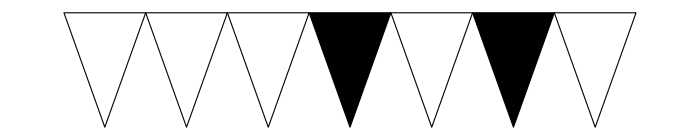

```mathematica
evenTriangles[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],r=rowLength[Length[initialConditions]][[2]]-1},
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*(i+1)]]]],EdgeForm[Black],
Triangle[{(i+1)*b1+b2,(i+1)*b1,i*b1+b2}]},
{i,0,r}]
];(* Generates the "even" traingles that can then be interpreted as Graphics objects. *)
Graphics[evenTriangles[basis,c],ImageSize->100*rowLength[Length[c]][[2]]]
```

```mathematica
triangleCAList[basis_,initialConditions_]:=
Riffle[
oddTriangles[basis,initialConditions],evenTriangles[basis,initialConditions]
];  (* Combines the lists of "odd" and "even" triangles into a new list. *)
```

New generation rule:

```mathematica
ruleTable[rule_Integer,neighborCount_Integer:5]:=Reverse[PadLeft[IntegerDigits[rule,2],2^neighborCount]]; (* Given a number and Moore neighborhood size generates a rule table. *)
```

```mathematica
nextStep[initialConditions_List,rule_Integer,neighborCount_Integer:5]:=Table[
ruleTable[rule,neighborCount][[FromDigits[
If[i<neighborCount/2,PadLeft[Take[initialConditions,{1,i+Floor[neighborCount/2]}],neighborCount],If[i>Total[r]-neighborCount/2,PadRight[Take[initialConditions,{i-Floor[neighborCount/2],Total[r]}],neighborCount],Take[initialConditions,{i-Floor[neighborCount/2],i+Floor[neighborCount/2]}]]],2]+1]]
,{i,1,Length[initialConditions]}]; (*Generates the state at time t+1 given state at time t. *)
```

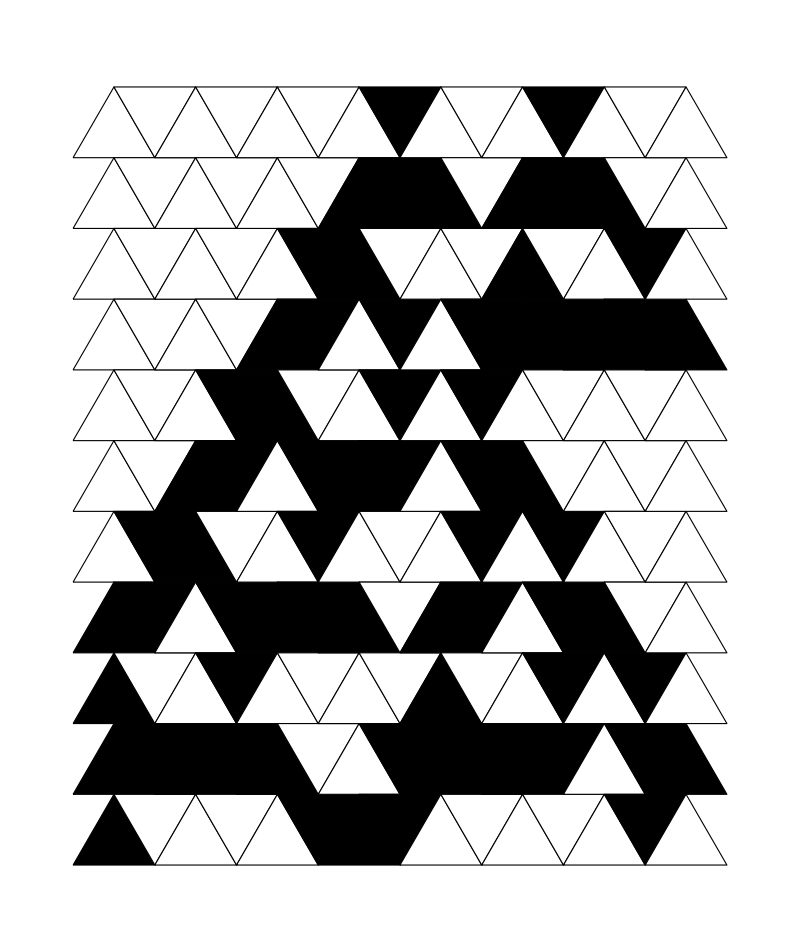

```mathematica
triangularCA[basis_,initialConditions_List,iterations_Integer,rule_Integer,neighborCount_Integer:5]:=Module[{d=basis[[1]][[2]]/2-basis[[2]][[2]],r=rowLength[Length[initialConditions]]},
Graphics[
Table[
Translate[triangleCAList[basis,Nest[nextStep[#,rule,neighborCount]&,initialConditions,i]],{0,d*i}],{i,0,iterations}
],
ImageSize->100*r[[1]]]
]; (* Plots a triangular CA *)
triangularCA[{{1,0},{0.5,Sqrt[3]/2}},c,10,30,3]
```